```mathematica
v="5";
p="0.1";
g5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/GapD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
v5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/velD-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number,Number,Number,Number}];
av5k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/Results/AveVel-l5k-v"<>v<>"-p0.1.txt",{Number,Number,Number,Number}];
```

```mathematica
g10kw=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-10k-wide.txt",{Number,Number,Number,Number,Number,Number}];
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-10k.txt",{Number,Number,Number,Number,Number,Number}];
g10kf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-10k-focus1.txt",{Number,Number,Number,Number,Number,Number}];
g20kw=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-20k-wide.txt",{Number,Number,Number,Number,Number,Number}];
g20k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-20k.txt",{Number,Number,Number,Number,Number,Number}];
g20kf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-20k-focus.txt",{Number,Number,Number,Number,Number,Number}];
g40kw=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-40k-wide.txt",{Number,Number,Number,Number,Number,Number}];
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-40k.txt",{Number,Number,Number,Number,Number,Number}];
g40kf=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-40k-focus.txt",{Number,Number,Number,Number,Number,Number}];
```

```mathematica
gap5v5=Table[{g5k1[[All,1]][[j]],Sum[g5k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g5k1]}];
```

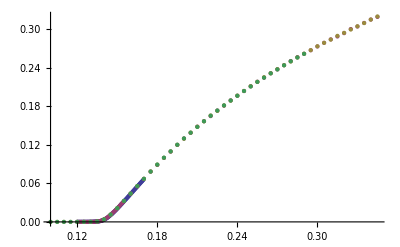

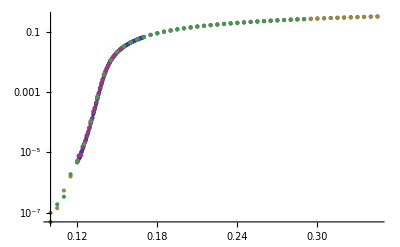

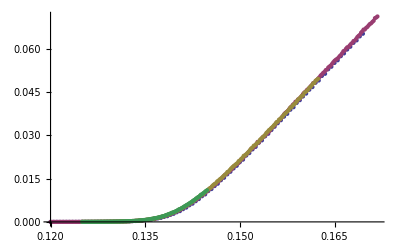

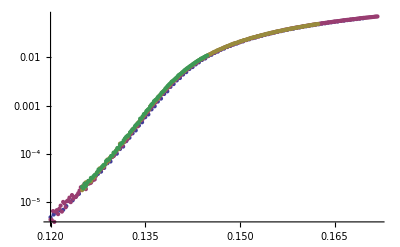

```mathematica
n=0;
gap10w=Table[{g10kw[[All,1]][[j]],Sum[g10kw[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g10kw]}];
gap10=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g10k1]}];
gap20=Table[{g20k1[[All,1]][[j]],Sum[g20k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g20k1]}];
gap20w=Table[{g20kw[[All,1]][[j]],Sum[g20kw[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g20kw]}];
gap10v5=Table[{g10kf[[All,1]][[j]],Sum[g10kf[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g10kf]}];
gap20v5=Table[{g20kf[[All,1]][[j]],Sum[g20kf[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g20kf]}];
gap40v5=Table[{g40kf[[All,1]][[j]],Sum[g40kf[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40kf]}];
gap40w=Table[{g40kw[[All,1]][[j]],Sum[g40kw[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40kw]}];
gap40=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40k1]}];
ListPlot[{gap5v5,gap10w,gap20w,gap40w}]
ListLogPlot[{gap5v5,gap10w,gap20w,gap40w},PlotRange->Full]
ListPlot[{gap5v5,gap10v5,gap20v5,gap40v5},PlotRange->Full]
ListLogPlot[{gap5v5,gap10v5,gap20v5,gap40v5},PlotRange->Full]
```

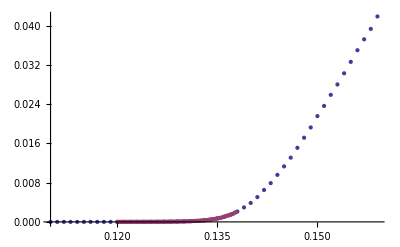

```mathematica
n=0;
g40k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-40k.txt",{Number,Number,Number,Number,Number,Number}];
g40k2=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v5-10k-focus.txt",{Number,Number,Number,Number,Number,Number}];
gap40=Table[{g40k1[[All,1]][[j]],Sum[g40k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40k1]}];
gap402=Table[{g40k2[[All,1]][[j]],Sum[g40k2[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g40k2]}];
ListPlot[{gap40,gap402},PlotRange->Full]
```

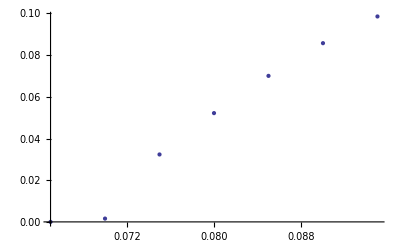

```mathematica
g10k1=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v11-10k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
n=0;
gap10=Table[{g10k1[[All,1]][[j]],Sum[g10k1[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[g10k1]}];
ListPlot[gap10]
```

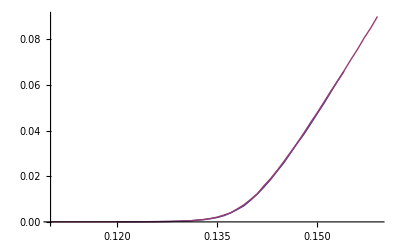

```mathematica
ListLinePlot[{gap10,gap20}]
```

```mathematica
gap100f=Table[{g10kf[[All,1]][[j]],Sum[g10kf[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10kf]}];
gap101f=Table[{g10kf[[All,1]][[j]],Sum[g10kf[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10kf]}];
gap102f=Table[{g10kf[[All,1]][[j]],Sum[g10kf[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10kf]}];
gap103f=Table[{g10kf[[All,1]][[j]],Sum[g10kf[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10kf]}];
gap104f=Table[{g10kf[[All,1]][[j]],Sum[g10kf[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10kf]}];
```

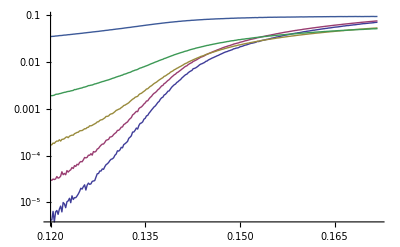

```mathematica
ListLogPlot[{gap100f,gap101f,gap102f,gap103f,gap104f},PlotRange->Full,Joined->True,PlotLegend->{"0","1","2","3","4"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
gap100=Table[{g10kw[[All,1]][[j]],Sum[g10kw[[All,i]][[j]],{i,2,2}]},{j,1,Length[g10kw]}];
gap101=Table[{g10kw[[All,1]][[j]],Sum[g10kw[[All,i]][[j]],{i,3,3}]},{j,1,Length[g10kw]}];
gap102=Table[{g10kw[[All,1]][[j]],Sum[g10kw[[All,i]][[j]],{i,4,4}]},{j,1,Length[g10kw]}];
gap103=Table[{g10kw[[All,1]][[j]],Sum[g10kw[[All,i]][[j]],{i,5,5}]},{j,1,Length[g10kw]}];
gap104=Table[{g10kw[[All,1]][[j]],Sum[g10kw[[All,i]][[j]],{i,6,6}]},{j,1,Length[g10kw]}];
gap200=Table[{g20kw[[All,1]][[j]],Sum[g20kw[[All,i]][[j]],{i,2,2}]},{j,1,Length[g20kw]}];
gap201=Table[{g20kw[[All,1]][[j]],Sum[g20kw[[All,i]][[j]],{i,3,3}]},{j,1,Length[g20kw]}];
gap202=Table[{g20kw[[All,1]][[j]],Sum[g20kw[[All,i]][[j]],{i,4,4}]},{j,1,Length[g20kw]}];
gap203=Table[{g20kw[[All,1]][[j]],Sum[g20kw[[All,i]][[j]],{i,5,5}]},{j,1,Length[g20kw]}];
gap204=Table[{g20kw[[All,1]][[j]],Sum[g20kw[[All,i]][[j]],{i,6,6}]},{j,1,Length[g20kw]}];
gap400=Table[{g40kw[[All,1]][[j]],Sum[g40kw[[All,i]][[j]],{i,2,2}]},{j,1,Length[g40kw]}];
gap401=Table[{g40kw[[All,1]][[j]],Sum[g40kw[[All,i]][[j]],{i,3,3}]},{j,1,Length[g40kw]}];
gap402=Table[{g40kw[[All,1]][[j]],Sum[g40kw[[All,i]][[j]],{i,4,4}]},{j,1,Length[g40kw]}];
gap403=Table[{g40kw[[All,1]][[j]],Sum[g40kw[[All,i]][[j]],{i,5,5}]},{j,1,Length[g40kw]}];
gap404=Table[{g40kw[[All,1]][[j]],Sum[g40kw[[All,i]][[j]],{i,6,6}]},{j,1,Length[g40kw]}];
```

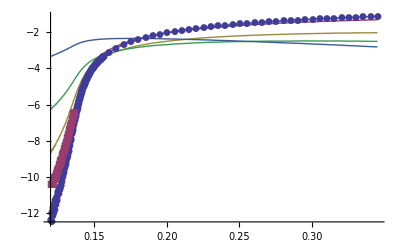

```mathematica
ListLogPlot[{gap100,gap101,gap102,gap103,gap104},PlotLegend->{"0","1","2","3","4"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
ListLogPlot[{gap100,gap101,gap102,gap103,gap104},PlotLegend->{"0","1","2","3","4"},LegendPosition->{1.1,-0.4},LegendShadow->None,Joined->{True},PlotMarkers->Automatic,PlotRange->Full]
```

-Graphics-

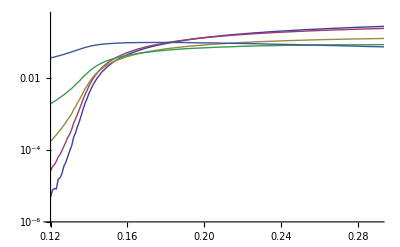

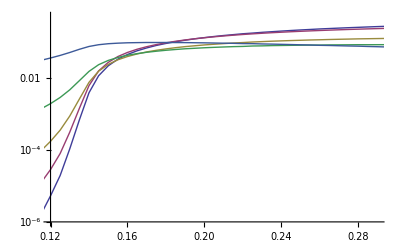

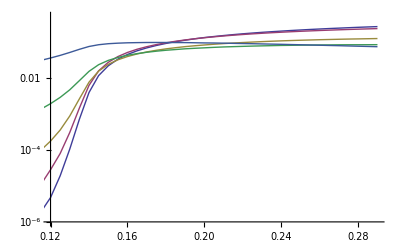

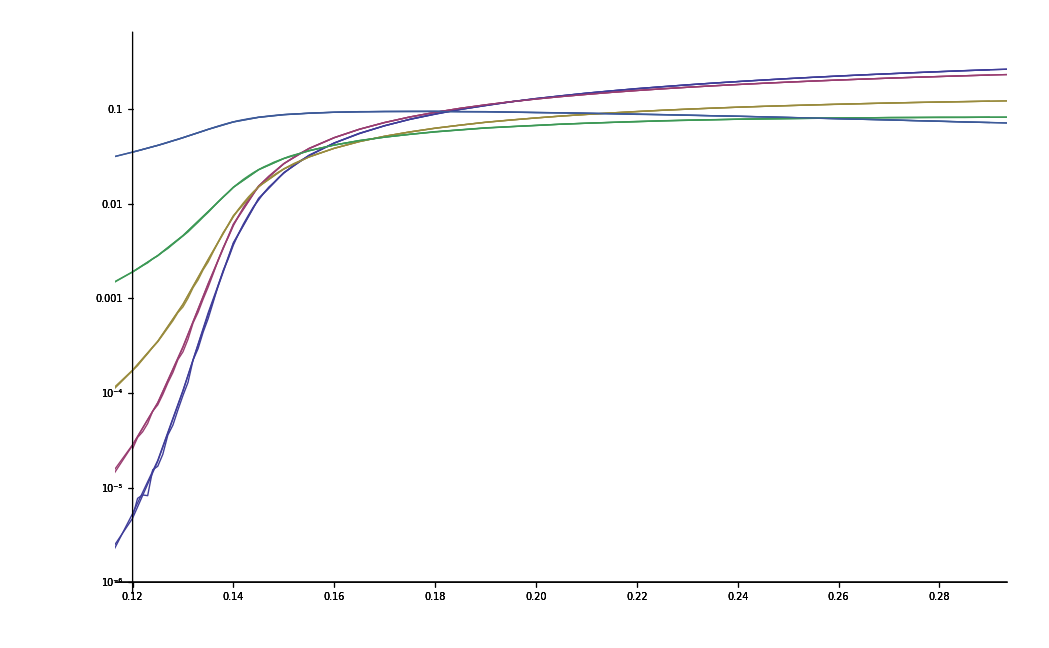

```mathematica
picc1=ListLogPlot[{gap100,gap101,gap102,gap103,gap104},PlotRange->{{0.12,0.29},{10^-6,0.5}},Joined->True,PlotLegend->{"0","1","2","3","4"},LegendPosition->{1.1,-0.4},LegendShadow->None]
picc2=ListLogPlot[{gap200,gap201,gap202,gap203,gap204},PlotRange->{{0.12,0.29},{10^-6,0.5}},Joined->True,PlotLegend->{"0","1","2","3","4"},LegendPosition->{1.1,-0.4},LegendShadow->None]
picc3=ListLogPlot[{gap400,gap401,gap402,gap403,gap404},PlotRange->{{0.12,0.29},{10^-6,0.5}},Joined->True,PlotLegend->{"0","1","2","3","4"},LegendPosition->{1.1,-0.4},LegendShadow->None]
Show[{picc1,picc2,picc3}]
```

```mathematica
test=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim/Scaling/v11-10k.txt",{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
n=0;
test1=Table[{test[[All,1]][[j]],Sum[test[[All,i]][[j]],{i,2,n+2}]},{j,1,Length[test]}];
```

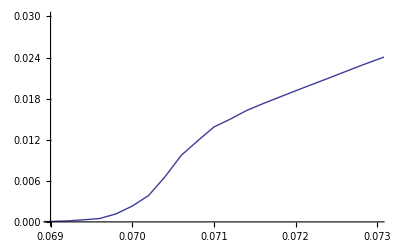

```mathematica
ListLinePlot[test1,PlotRange->{{0.069,0.073},{0,0.03}}]
```

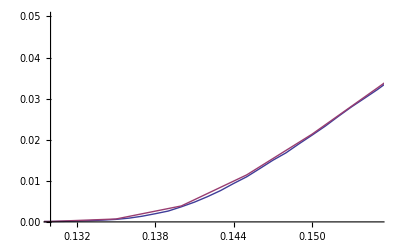

```mathematica
ListLinePlot[{gap10w,gap40w},PlotRange->{{0.13,0.155},{0,0.05}}]
```